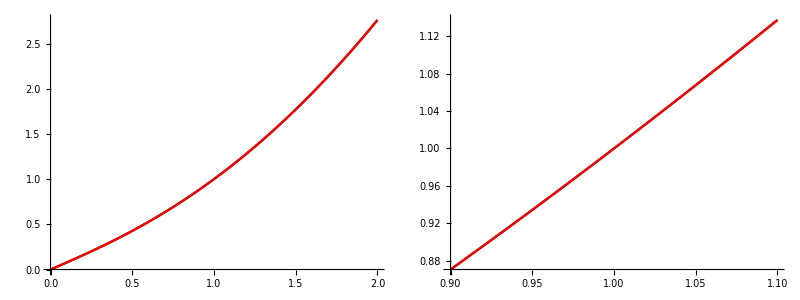

0.0005624737680297483 + x*(0.7797825941381623 + x*(0.025694875450339216 + 
         x*(0.32086022134934217 + x*(-0.19450407011549792 + 
               x*(0.09353199402114554 + x*(-0.032113982358561236 + (0.006866621222216209 - 0.0006807274751769723*x)*x))))))

```mathematica
dx=0.01;
H[x_]=0.5*(x^2+ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.)));
Hexpand[x_]=Normal[Series[H[x],{x,1,8}]]//FullSimplify;
Happrox[x_]=Piecewise[{{0.5*(x^2+ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.))),0<x<1-dx},{Hexpand[x],1-dx<x<1+dx},{0.5*(x^2+ArcTanh[√(1.-1./x^2)]/(√(1.-1./x^2))),x>1+dx}}];

Hexpand[x]//CForm

Grid[{{Plot[{H[x],Happrox[x]},{x,0,2},PlotStyle->{Black,Red},ImageSize->400],Plot[{H[x],Happrox[x]},{x,1-10dx,1+10dx},PlotStyle->{Black,Red},ImageSize->400]}}]
```

```mathematica
HT[x_]=(x^2+(1.-2. x^2)ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.)))/(1.-x^2);
HTapprox[x_]=Piecewise[{{(x^2+(1.-2. x^2)ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.)))/(1.-x^2),0<x<1-dx},{-0.003202301654317485+x*(1.6035437558657903+x*(-0.15518846478629494+x*(-0.32881655667957355+x*(0.3837277273799249+x*(-0.2432341652146951+x*(0.09666948118913454+(-0.0225216819642642+0.002355539197625668*x)*x)))))),1-dx<x<1+dx},{(x^2+(1.-2. x^2)ArcTanh[√(1.-1./x^2)]/(√(1.-1./x^2)))/(1.-x^2),x>1+dx}}];

(* For some reason there's a numerically small pole term. I removed by hand *)
HTexpand[x_]=Normal[Series[HT[x],{x,1,8}]]//Expand

(-0.003202301654317485+1.6035437558657903 x-0.15518846478629494 x^2-0.32881655667957355 x^3+0.3837277273799249 x^4-0.2432341652146951 x^5+0.09666948118913454 x^6-0.0225216819642642 x^7+0.002355539197625668 x^8)//FullSimplify//CForm

Grid[{{Plot[{HT[x],HTapprox[x]},{x,0,2},PlotStyle->{Black,Red},ImageSize->400],Plot[{HT[x],HTapprox[x]},{x,1-10dx,1+10dx},PlotStyle->{Black,Red},ImageSize->400]}}]
```

-0.0032023-(8.88178×10^-16)/(-1+x)+1.60354 x-0.155188 x^2-0.328817 x^3+0.383728 x^4-0.243234 x^5+0.0966695 x^6-0.0225217 x^7+0.00235554 x^8

-0.003202301654317485 + x*(1.6035437558657903 + x*(-0.15518846478629494 + 
         x*(-0.32881655667957355 + x*(0.3837277273799249 + x*
                (-0.2432341652146951 + x*(0.09666948118913454 + (-0.0225216819642642 + 0.002355539197625668*x)*x))))))

0.00437237+(8.88178×10^-16)/(-1+x)-0.0443396 x+0.207842 x^2+0.96801 x^3-0.769577 x^4+0.427771 x^5-0.159634 x^6+0.0358939 x^7-0.00367187 x^8

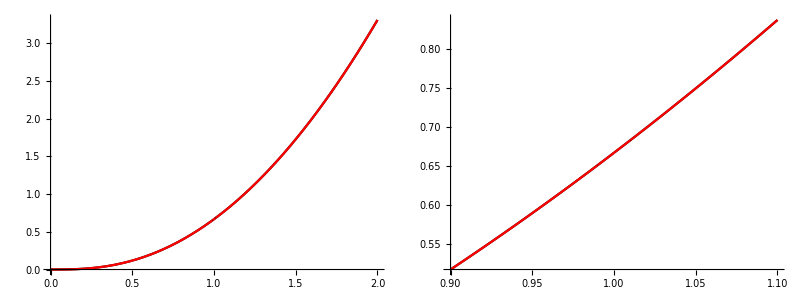

0.004372373412624753 + x*(-0.04433956136745337 + x*(0.2078416939099339 + 
         x*(0.9680100429323358 + x*(-0.7695771720535178 + x*
                (0.42777119681106374 + x*(-0.15963396768329577 + (0.03589393063070768 - 0.0036718699257309944*x)*x))))))

```mathematica
HL[x_]=x^2/(1.-x^2)(-x^2+ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.)));
HLapprox[x_]=Piecewise[{{x^2/(1.-x^2)(-x^2+ArcTan[√(1./x^2-1.)]/(√(1./x^2-1.))),0<x<1-dx},{0.004372373412624753+x*(-0.04433956136745337+x*(0.2078416939099339+x*(0.9680100429323358+x*(-0.7695771720535178+x*(0.42777119681106374+x*(-0.15963396768329577+(0.03589393063070768-0.0036718699257309944*x)*x)))))),1-dx<x<1+dx},{x^2/(1.-x^2)(-x^2+ArcTanh[√(1.-1./x^2)]/(√(1.-1./x^2))),x>1+dx}}];

(* For some reason there's a numerically small pole term. I removed by hand *)
HLexpand[x_]=Normal[Series[HL[x],{x,1,8}]]//Expand

(0.004372373412624753-0.04433956136745337 x+0.2078416939099339 x^2+0.9680100429323358 x^3-0.7695771720535178 x^4+0.42777119681106374 x^5-0.15963396768329577 x^6+0.03589393063070768 x^7-0.0036718699257309944 x^8)//FullSimplify//CForm

Grid[{{Plot[{HL[x],HLapprox[x]},{x,0,2},PlotStyle->{Black,Red},ImageSize->400],Plot[{HL[x],HLapprox[x]},{x,1-10dx,1+10dx},PlotStyle->{Black,Red},ImageSize->400]}}]
```

```mathematica
H[x_]=1/2*(x^2+ArcTan[√(1/x^2-1)]/(√(1/x^2-1)));

HT[x_]=(x^2+(1-2 x^2)ArcTan[√(1/x^2-1)]/(√(1/x^2-1)))/(1-x^2);

HL[x_]=x^2/(1-x^2)(-x^2+ArcTan[√(1/x^2-1)]/(√(1/x^2-1)));

Clear[a]

Limit[((HT[a*x]/2)-HL[a*x])/H[x],x->0]
```

1/(√(1/a^2))

```mathematica
dx=0.01;
H240[x_]=x^4/((x^2-1.)^2)*(2. + x^2 - (3.*ArcTan[√(1./x^2-1.)])/(√(1./x^2-1.)));
Hexpand[x_]=Normal[Series[H240[x],{x,1,8}]]//Expand
```

-0.00508763+(1.33227×10^-15)/(-1+x)^2+(3.9968×10^-15)/(-1+x)+0.0569588 x-0.301891 x^2+1.01947 x^3-0.504755 x^4+0.163923 x^5-0.030831 x^6+0.00206225 x^7+0.000154604 x^8

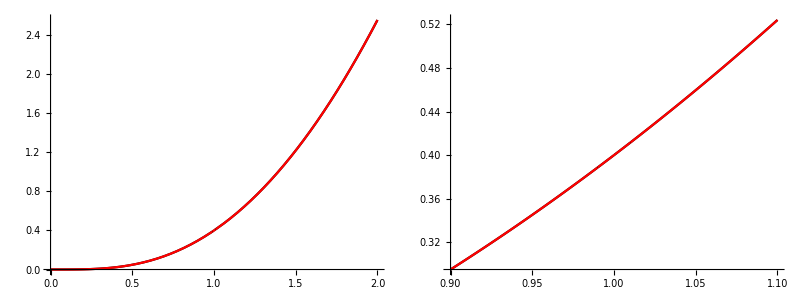

-0.005087625772544818 + x*(0.05695884534842821 + x*(-0.3018911943816236 + 
         x*(1.019465776582752 + x*(-0.5047550486743451 + x*(0.16392338295963027 + 
                  x*(-0.030830985240682104 + (0.0020622455600826832 + 0.0001546036183062223*x)*x))))))

0.4

```mathematica
Happrox[x_]=Piecewise[{{x^4/((x^2-1.)^2)*(2. + x^2 - (3.*ArcTan[√(1./x^2-1.)])/(√(1./x^2-1.))),0<x<1-dx},{-0.005087625772544818+0.05695884534842821 x-0.3018911943816236 x^2+1.019465776582752 x^3-0.5047550486743451 x^4+0.16392338295963027 x^5-0.030830985240682104 x^6+0.0020622455600826832 x^7+0.0001546036183062223 x^8,1-dx<x<1+dx},{x^4/((x^2-1.)^2)*(2. + x^2 - (3.*ArcTanh[√(1.-1./x^2)])/(√(1.-1./x^2))),x>1+dx}}];

(-0.005087625772544818+0.05695884534842821 x-0.3018911943816236 x^2+1.019465776582752 x^3-0.5047550486743451 x^4+0.16392338295963027 x^5-0.030830985240682104 x^6+0.0020622455600826832 x^7+0.0001546036183062223 x^8)//FullSimplify//CForm

Grid[{{Plot[{H240[x],Happrox[x]},{x,0,2},PlotStyle->{Black,Red},ImageSize->400],Plot[{H240[x],Happrox[x]},{x,1-10dx,1+10dx},PlotStyle->{Black,Red},ImageSize->400]}}]
```